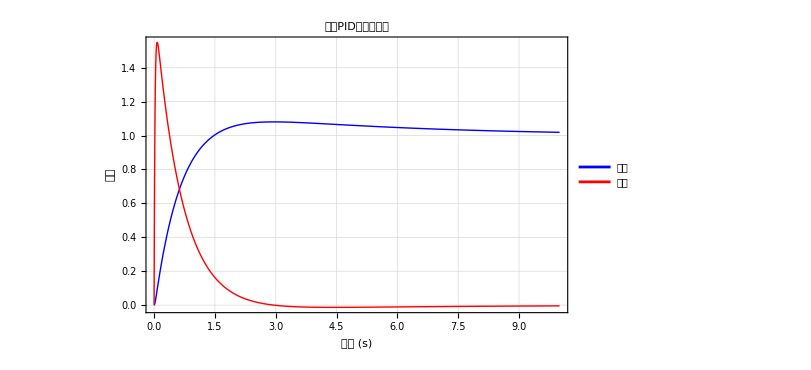

```mathematica
ClearAll["Global`*"]

(*系统参数*)
{a,b,c,d}={({{0,1},{0,0}}),({{0},{1}}),({{1,0},{0,1}}),({{0},{0}})};

(*可调节的PID参数*)
Kp1=10;   (*外环比例增益*)
Ki1=2;    (*外环积分增益*)
Kd1=5;    (*外环微分增益*)
Kp2=8;    (*内环比例增益*)
Ki2=3;    (*内环积分增益*)

(*仿真参数*)
reference=1;      (*参考输入*)
initialPos=0;     (*初始位置*)
initialVel=0;     (*初始速度*)
tmax=10;          (*仿真时间*)

(*串级PID控制器仿真*)
cascadePID[kp1_,ki1_,kd1_,kp2_,ki2_,ref_,x0pos_,x0vel_,tmax_]:=Module[{sol},sol=NDSolve[{(*系统动态方程*)x1'[t]==x2[t],x2'[t]==kp2*(kp1*(ref-x1[t])+ki1*x3[t]+kd1*(-x2[t])-x2[t])+ki2*x4[t],(*积分项*)x3'[t]==ref-x1[t],x4'[t]==kp1*(ref-x1[t])+ki1*x3[t]+kd1*(-x2[t])-x2[t],(*初始条件*)x1[0]==x0pos,x2[0]==x0vel,x3[0]==0,x4[0]==0},{x1,x2,x3,x4},{t,0,tmax}];
If[sol==={},Print["求解失败！"];{{0,0,0,0}},{x1[t],x2[t],x3[t],x4[t]}/. sol[[1]]]];

(*执行仿真*)
{position,velocity,int1,int2}=cascadePID[Kp1,Ki1,Kd1,Kp2,Ki2,reference,initialPos,initialVel,tmax];

(*绘制结果*)
Plot[{position,velocity},{t,0,tmax},PlotRange->All,PlotStyle->{{Blue,Thick},{Red,Thick}},PlotLegends->{"位置","速度"},PlotLabel->"串级PID控制器响应",FrameLabel->{"时间 (s)","状态"},Frame->True,GridLines->Automatic,ImageSize->600]
```